```mathematica
h=π/400.;
```

```mathematica
SplitLine[a_List,b_List,h_,OptionsPattern[{FirstPoint->True,LastPoint->True}]]:=Module[{dr,np,i,j},np=Ceiling[Norm[b-a]/h];dr=(b-a)/np;(*Print[np];Print[dr];*)
i=If[OptionValue[FirstPoint],0,1];
j=If[OptionValue[LastPoint],np,np-1];
Table[a+q dr,{q,i,j}]]
```

```mathematica
pts={{6.3,0},{6.3,0.6},{-0.2,0.6},{-0.5,0.3},{-3.5,0.3},{-3.5,0},{-3.5,-0.3},{-0.5,-0.3},{-0.2,-0.6},{6.3,-0.6},{6.3,0}};
```

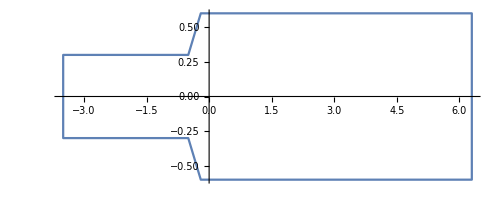

```mathematica
ListLinePlot[pts,AspectRatio->Automatic]
```

```mathematica
vertex=Flatten[Table[SplitLine[pts[[i]],pts[[i+1]],h,LastPoint->False],{i,Length@pts-1}],1];
```

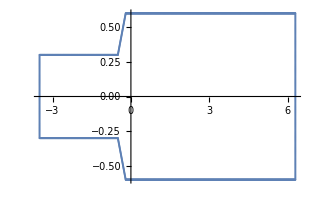

```mathematica
ListPlot[vertex,AspectRatio->Automatic]
```

```mathematica
n=Length@vertex;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["tube",
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.5    |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2019/02/20     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2019 Ilia Marchevsky, Kseniia Kuzmina, Evgeniya Ryatina  |
*-----------------------------------------------------------------------------*
| File name: tube"<>StringRepeat[" ",61]<>"|
| Info: tube airfoil (for internal flow) ("<>ToString[n]<>" panels)"<>StringRepeat[" ",28-StringLength@ToString[n]]<>"|
\\*---------------------------------------------------------------------------*/ 
"}~Join~{"r = {"}
~Join~
Table[{"{",vertex[[i,1]],",",vertex[[i,2]],"},"},{i,n-1}]
~Join~
{{"{",vertex[[-1,1]],",",vertex[[-1,2]],"}"}}
,"Table"]
```

tube